```mathematica
a=0;b=1;
```

peak[x_] = Piecewise[{{h - Abs[x - t - h], t <= x <= t + 2 h}}, 0]

D[peak[x], x]

t = 0.5; h = 0.1; Plot[peak[x], {x, a, b}, AspectRatio -> 1, PlotRange -> Full]

Clear[t, h]

```mathematica
peak[x_]=Piecewise[{{x-t,t≤x≤t+h},{t+2h-x,t+h≤x≤t+2h}},0]
```

Piecewise[{{-t+x, t≤x≤h+t}, {2 h+t-x, h+t≤x≤2 h+t}, {0, True}}]

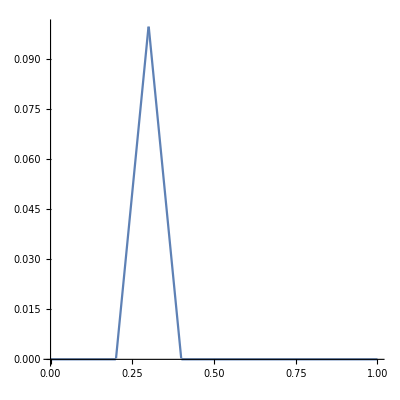

```mathematica
t=0.2;h=0.1;Plot[peak[x],{x,a,b},AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[t,h]
```

```mathematica
p1[x_]=(x-t)
```

-t+x

```mathematica
p2[x_]=t+2h-x
```

2 h+t-x

```mathematica
0==p1[t]
```

True

```mathematica
p1[t+h]==p2[t+h]
```

True

```mathematica
p2[t+2h]==0
```

True

```mathematica
peakp1[x_]=D[peak[x],x]
```

Piecewise[{{1, t-x≤0&&h+t-x≥0}, {-1, h+t-x≤0&&2 h+t-x≥0}, {0, True}}]

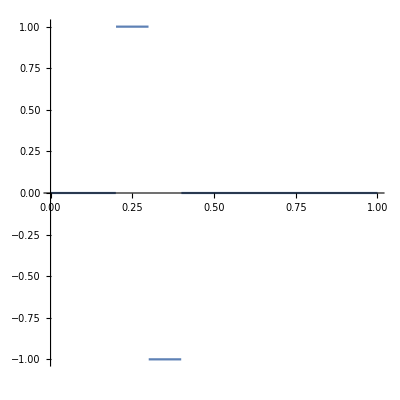

```mathematica
t=0.2;h=0.1;Plot[peakp1[x],{x,a,b},AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[t,h]
```

```mathematica
p1p1[x_]=D[p1[x],x]
```

1

```mathematica
p2p1[x_]=D[p2[x],x]
```

-1

```mathematica
intpeak[x_]=Integrate[peak[x],x]
```

Piecewise[{{-t x+x^2/2, t-x≤0&&h+t-x≥0}, {2 h x+t x-x^2/2, h+t-x≤0&&2 h+t-x≥0}, {0, True}}]

```mathematica
Simplify[Integrate[p1[x],{x,t,t+h}]+Integrate[p2[x],{x,t+h,t+2h}]]
```

h^2

```mathematica
Simplify[peak[x]]
```

Piecewise[{{-t+x, t≤x≤h+t}, {2 h+t-x, h+t≤x≤2 h+t}, {0, True}}]

```mathematica
showpeak[x_,t_,h_]=Piecewise[{{x-t,t≤x≤t+h},{t+2h-x,t+h≤x≤t+2h}},0]
```

Piecewise[{{-t+x, t≤x≤h+t}, {2 h+t-x, h+t≤x≤2 h+t}, {0, True}}]

```mathematica
c[h_]=1.5/(1-h/0.1)
```

1.5/(1-10. h)

```mathematica
twopk[x_,t_,h_]=showpeak[x,0,0.1]+3(c[h]-1)/4*showpeak[x,t,h]
```

(Piecewise[{{x, 0≤x≤0.1}, {0.2-x, 0.1≤x≤0.2}, {0, True}}])+3/4 (-1+1.5/(1-10. h)) (Piecewise[{{-t+x, t≤x≤h+t}, {2 h+t-x, h+t≤x≤2 h+t}, {0, True}}])

```mathematica
showtwopk[x_]=twopk[x,0.5,0.05]
```

1.5 (Piecewise[{{-0.5+x, 0.5≤x≤0.55}, {0.6-x, 0.55≤x≤0.6}, {0, True}}])+(Piecewise[{{x, 0≤x≤0.1}, {0.2-x, 0.1≤x≤0.2}, {0, True}}])

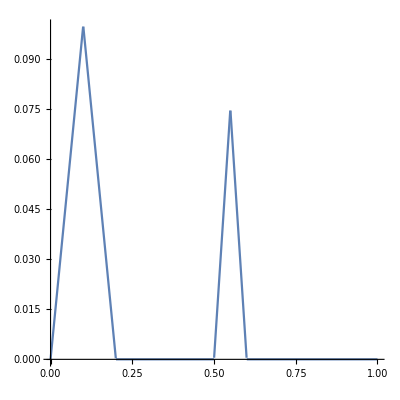

```mathematica
Plot[showtwopk[x],{x,0,1},AspectRatio->1,PlotRange->Full]
```